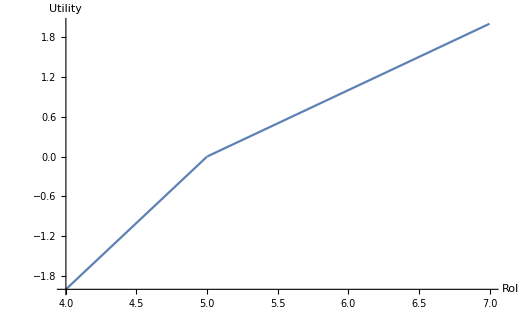

```mathematica
Plot[Max[x-5,0]-2Max[5-x,0],{x,4,7},AxesLabel->{"RoI","Utility"},AxesOrigin->{4,-2},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14}]
```

```mathematica
stocks={"MSFT","AAPL","GOOG"};
y=2015;
```

```mathematica
ans=solveObjective[{"MSFT","AAPL","GOOG"},2015]
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
q=ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

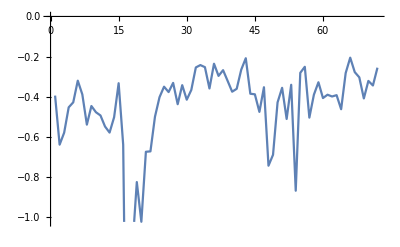

```mathematica
ListLinePlot[xs.ans]
```

```mathematica
rangeVars[q,7]
```

{q$1,q$2,q$3,q$4,q$5,q$6,q$7}

```mathematica
ans=%
```

{q$1→-0.462577,q$2→0.0813624,q$3→0.118456,q$4→0.0476892,q$5→0.0255442,q$6→0.145512,q$7→-0.860971}

```mathematica
rangeVars[q,7]/.ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
xs=adjustFeaturesMatrix[x[y]/@stocks];
rs=Flatten[r[y]/@stocks,1];
```

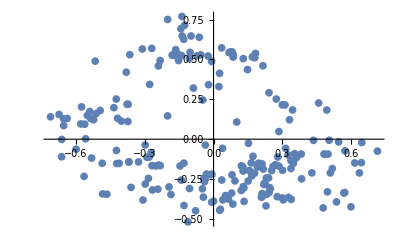

```mathematica
ListPlot@
Flatten[
Map[Function[xStock,
(*#[[3;;4]]&/@xStock]*)
Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,#[[3;;4]]&/@xStock]],
xs],
1]
```

```mathematica
{a,b,c}≥{1,2,3}
```

{4,b,c}≥{1,2,3}

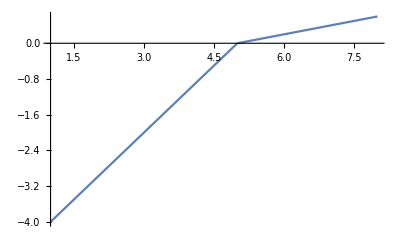

```mathematica
U[p_]:=0.2 (p-5)+Min[(1-0.2)*(p-5),0];
Plot[U[p],{p,1,8}]
```

```mathematica
stocks={"AAPL"};
y=2015;
```

```mathematica
solveObjective[stocks,y]
```

{-0.0281717,0.0000942056,0.0140221,0.0384223,0.0010725,-0.0246407,0.00887866,-0.00381048,-0.0271403,-0.00777011,0.0257572,0.00763432,0.0260156,0.00516014,0.00106206,-0.0350132,0.0565328,0.0311335,-0.0146341,0.0125469,0.000168664,0.00766959,0.0110841,-0.00842088,0.00664256,0.0192115,0.0234388,0.0126521,0.00490274,0.00590179,0.00696237,-0.00209758,0.00817439,0.027027,-0.0062406,-0.0255732,0.0126563,-0.0150283,0.00490417,0.00209156,-0.00633898,-0.0165706,0.00150305,0.0042654,-0.0206859,-0.0182315,0.0180792,-0.00691041,0.0110041,0.0167267,0.0112563,-0.0075504,-0.012549,0.0104051,-0.00408773,-0.0261268,0.00697034,-0.00796845,0.0253144,-0.0153517,-0.0014466,0.00861167,0.0161985,-0.0105222,-0.00325371,0.00764331,0.00426675,-0.00196696,-0.00433583,0.00380048,-0.00481148,-0.0112547,0.0228457}

```mathematica
Times[a,b,c]
```

a b c

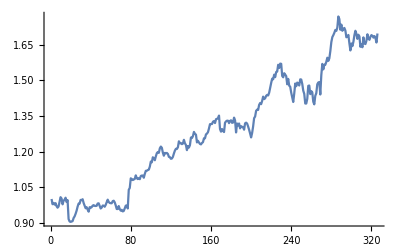

```mathematica
ListLinePlot[rawReturns["AAPL",2014]]
```

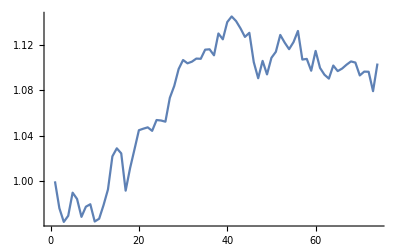

```mathematica
ListLinePlot[rawReturns[{"AAPL","GOOGL"},2015]]
```

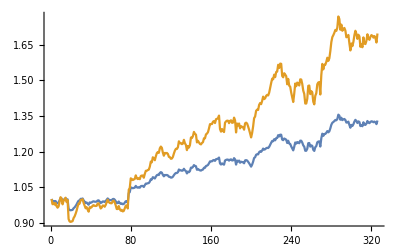

```mathematica
ListLinePlot[{rawReturns[{"AAPL"},2014,{0.5,0.5}],rawReturns["AAPL",2014]}]
```

```mathematica
stocks={"AAPL"};
y=2015;
```

```mathematica
solveObjective[stocks,y]
```

>>  
Calling SDPT3 4.0: 155 variables, 74 equality constraints
------------------------------------------------------------

 num. of constraints = 74
 dim. of linear var  = 148
 dim. of free   var  =  7 *** convert ublk to lblk
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
    NT      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|3.3e-03|1.6e+01|2.5e+04| 9.002489e+02  0.000000e+00| 0:0:00| chol  1  1 
 1|1.000|0.971|3.2e-06|5.5e-01|1.5e+03| 8.155585e+02  1.342449e-02| 0:0:00| chol  1  1 
 2|0.993|0.468|2.7e-06|3.0e-01|6.4e+02| 4.033384e+02  1.328559e-02| 0:0:00| chol  1  1 
 3|0.888|0.535|2.1e-06|1.4e-01|2.9e+02| 1.908799e+02  1.228593e-02| 0:0:00| chol  1  1 
 4|0.435|0.283|2.3e-06|1.0e-01|2.2e+02| 1.309598e+02  1.167470e-02| 0:0:00| chol  1  1 
 5|1.000|0.551|3.4e-07|4.5e-02|1.4e+02| 8.264861e+01  1.097780e-02| 0:0:00| chol  1  1 
 6|1.000|0.670|1.7e-07|1.5e-02|6.6e+01| 4.411851e+01  1.033070e-02| 0:0:00| chol  1  1 
 7|1.000|0.519|7.9e-08|7.1e-03|2.8e+01| 1.959968e+01  1.007692e-02| 0:0:00| chol  1  1 
 8|0.989|0.384|4.3e-08|4.4e-03|1.6e+01| 1.278230e+01  9.931736e-03| 0:0:00| chol  1  1 
 9|1.000|0.480|4.6e-09|2.3e-03|5.7e+00| 4.863129e+00  9.839697e-03| 0:0:00| chol  1  1 
10|1.000|0.695|5.8e-10|7.0e-04|1.1e+00| 1.067393e+00  9.773091e-03| 0:0:00| chol  1  1 
11|0.939|0.448|3.6e-11|3.8e-04|1.5e-01| 1.502784e-01  9.797787e-03| 0:0:00| chol  1  1 
12|1.000|0.742|2.1e-11|9.9e-05|2.4e-02| 3.287641e-02  1.005629e-02| 0:0:00| chol  1  1 
13|1.000|0.603|3.9e-11|3.9e-05|1.2e-02| 2.315748e-02  1.117506e-02| 0:0:00| chol  1  1 
14|1.000|0.274|3.5e-11|3.1e-05|7.7e-03| 1.912998e-02  1.161907e-02| 0:0:00| chol  1  1 
15|1.000|0.673|5.0e-12|1.3e-05|4.4e-03| 1.690453e-02  1.260826e-02| 0:0:00| chol  1  1 
16|1.000|0.867|7.1e-13|5.4e-06|2.2e-03| 1.525804e-02  1.309793e-02| 0:0:00| chol  1  1 
17|1.000|0.624|6.8e-13|2.7e-06|1.1e-03| 1.445518e-02  1.340445e-02| 0:0:00| chol  1  1 
18|1.000|0.892|1.6e-13|1.3e-06|5.0e-04| 1.414187e-02  1.364425e-02| 0:0:00| chol  1  1 
19|0.918|0.926|1.7e-13|6.1e-07|1.1e-04| 1.390592e-02  1.379500e-02| 0:0:00| chol  1  1 
20|0.950|0.940|3.1e-13|1.4e-07|3.7e-05| 1.386010e-02  1.382351e-02| 0:0:00| chol  1  1 
21|1.000|0.984|1.5e-13|4.4e-08|1.8e-06| 1.384091e-02  1.383918e-02| 0:0:00| chol  1  1 
22|1.000|0.989|7.9e-15|2.1e-09|3.3e-08| 1.384011e-02  1.384008e-02| 0:0:00| chol  1  1 
23|1.000|0.989|6.8e-15|4.0e-11|5.8e-10| 1.384010e-02  1.384010e-02| 0:0:00|
  stop: max(relative gap, infeasibilities) < 1.49e-08
-------------------------------------------------------------------
 number of iterations   = 23
 primal objective value =  1.38401016e-02
 dual   objective value =  1.38401011e-02
 gap := trace(XZ)       = 5.76e-10
 relative gap           = 5.60e-10
 actual relative gap    = 5.33e-10
 rel. primal infeas (scaled problem)   = 6.80e-15
 rel. dual     "        "       "      = 3.98e-11
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 1.2e-01, 5.9e+00, 8.4e+00
 norm(A), norm(b), norm(C) = 1.3e+01, 1.0e+00, 9.6e+00
 Total CPU time (secs)  = 0.17  
 CPU time per iteration = 0.01  
 termination code       =  0
 DIMACS: 6.8e-15  0.0e+00  1.9e-10  0.0e+00  5.3e-10  5.6e-10
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Solved
Optimal value (cvx_optval): -0.0208853

{0.0388709,0.0340096,0.0551056,-0.0819132,-0.000809325,0.0543623,-0.00114235}

```mathematica
trainingStocks={"MSFT","GOOGL","YHOO","AMZN"};
trainingYears=2005;
testStock="AAPL";
testYear=2014;
```

```mathematica
{ϕ,A,b}=Φ[x[trainingYears]/@trainingStocks];
```

Calling financial feeds

Calling financial feeds

Calling financial feeds

«1 more identical outputs»

```mathematica
rs=Flatten[r[trainingYears]/@trainingStocks,1];
```

Calling returns values for MSFT

Calling returns values for GOOGL

Calling returns values for YHOO

Calling returns values for AMZN

```mathematica
q=Last@cvxSolve[ϕ,rs];
```

>>  
Calling SDPT3 4.0: 20735 variables, 10364 equality constraints
------------------------------------------------------------

 num. of constraints = 10364
 dim. of linear var  = 20728
 dim. of free   var  =  7 *** convert ublk to lblk
 number of dense column in A = 14
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
    NT      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|6.0e-07|2.0e+02|4.3e+08| 1.492128e+06  0.000000e+00| 0:0:00| spchol  1  1 
 1|1.000|0.934|3.7e-05|1.4e+01|3.0e+07| 1.475436e+06  0.000000e+00| 0:0:00| spchol  1  1 
 2|1.000|0.043|1.9e-04|1.3e+01|4.7e+07| 2.382208e+06  0.000000e+00| 0:0:00| spchol  1  1 
 3|1.000|0.949|6.5e-06|7.8e-01|4.5e+06| 2.130252e+06  0.000000e+00| 0:0:00| spchol  1  1 
 4|1.000|0.953|3.8e-06|9.6e-02|7.2e+05| 6.327077e+05  0.000000e+00| 0:0:00| spchol  1  1 
 5|0.985|0.442|6.4e-08|6.7e-02|6.9e+04| 6.325770e+04  0.000000e+00| 0:0:00| spchol  1  1 
 6|0.989|0.836|1.9e-09|1.9e-02|2.9e+03| 2.778015e+03  0.000000e+00| 0:0:00| spchol  2  1 
 7|0.969|0.986|1.8e-08|1.2e-03|1.2e+02| 1.173959e+02  0.000000e+00| 0:0:00| spchol  2  2 
 8|0.989|1.000|2.0e-10|9.4e-05|1.3e+00| 1.297038e+00  0.000000e+00| 0:0:00| spchol  2  2 
 9|0.989|1.000|2.4e-12|9.4e-06|1.4e-02| 1.424383e-02  0.000000e+00| 0:0:00| spchol  3  2 
10|0.998|1.000|1.0e-11|9.4e-07|1.8e-04| 1.824788e-04  0.000000e+00| 0:0:00| spchol * 5 * 4 
11|0.999|1.000|4.9e-13|9.4e-08|2.0e-06| 2.035774e-06  0.000000e+00| 0:0:01| spchol 21 12 
  stop: primal infeas has deteriorated too much, 1.3e-02
12|0.998|0.444|4.9e-13|9.4e-08|2.0e-06| 2.035774e-06  0.000000e+00| 0:0:01|
-------------------------------------------------------------------
 number of iterations   = 12
 primal objective value =  2.03577354e-06
 dual   objective value =  0.00000000e+00
 gap := trace(XZ)       = 2.04e-06
 relative gap           = 2.04e-06
 actual relative gap    = 2.04e-06
 rel. primal infeas (scaled problem)   = 4.88e-13
 rel. dual     "        "       "      = 9.37e-08
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 2.9e-08, 5.1e+01, 7.2e+01
 norm(A), norm(b), norm(C) = 1.5e+02, 1.0e+00, 1.0e+02
 Total CPU time (secs)  = 0.61  
 CPU time per iteration = 0.05  
 termination code       = -7
 DIMACS: 4.9e-13  0.0e+00  1.9e-06  0.0e+00  2.0e-06  2.0e-06
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Inaccurate/Solved
Optimal value (cvx_optval): -2.03577e-06

```mathematica
q
```

{1.55996×10^-9,-2.87452×10^-10,4.19348×10^-10,-1.39826×10^-10,-1.40852×10^-10,-1.3257×10^-10,-1.43223×10^-10}

```mathematica
testingXs=x[testYear][testStock];
```

Calling financial features feeds for AAPL

```mathematica
testingΦ=Φ[testingXs,A,b];
```

```mathematica
p=testingΦ.q;
```

```mathematica
testReturns=r[testYear][testStock];
```

Calling returns values for AAPL

```mathematica
actualReturns=testReturns*p+Rf*(1-p);
```

Calling returns values for AAPL

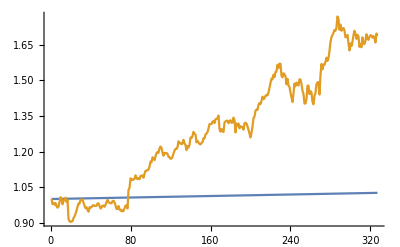

```mathematica
ListLinePlot[{FoldList[Times,1,1+actualReturns],rawReturns[testStock,testYear]}]
```

```mathematica
Length[rawReturns[testStock,testYear]]
```

Calling returns values for AAPL

327

```mathematica
Length[FoldList[Times,1,1+actualReturns]]
```

327

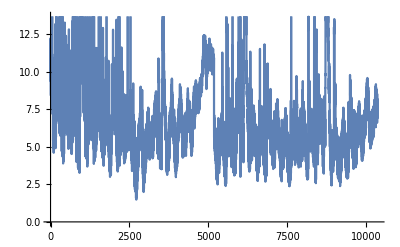

```mathematica
ListLinePlot[Norm/@ϕ]
```

```mathematica
testModel[trainingStocks,trainingYears,testStock,testYear]
```

Calling financial features feeds for MSFT

Calling financial features feeds for GOOGL

Calling financial features feeds for YHOO

Calling financial features feeds for AMZN

Set::shape: Lists {Φ$95812, A$95812, b$95812} and Φ$95812[{{{1., 1., 0.0826372, 0.134333, 6.50029×10^7}, {2., 1., 0.0810002, 0.115019, 1.09442×10^8}, {3., 1., 0.0759875, 0.114432, 7.24635×10^7}, « 46 », {2., 11., 0.0938117, 0.0994275, 7.14694×10^7}, « 2541 »}, {« 1 »}, {« 1 »}, {« 1 », « 49 », « 2541 »}}] are not the same shape.

Calling returns values for MSFT

Calling returns values for GOOGL

$Aborted[]

Calling returns values for YHOO.

Calling returns values for AMZN

Calling financial features feeds for AAPL

Calling returns values for AAPL

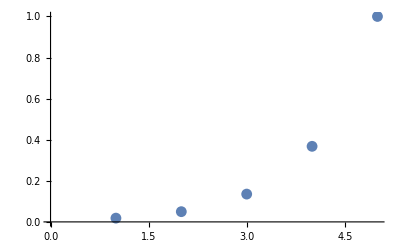

```mathematica
ListPlot[s[0][Range@5]]
```

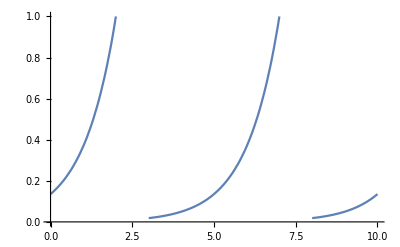

1.

```mathematica
s[d_]:=Function[x,
Exp[1(Mod[x-d,5,1]-5)],
{Listable}];

Plot[s[2][x],{x,0,10},PlotRange->{0,1}]
s[5][5.]
```

```mathematica
Mod[6,5,1]
```

1

```mathematica
Mod[7,5,1]
```

2

```mathematica
dayFeature[Range[5]]
```

Function[x$,Exp[μ_s (Mod[x$-{1,2,3,4,5},5,1]-5)],{Listable}]

```mathematica
stocks={"MSFT","AAPL","GOOGL","BA","KO","MCD","CAT"};
y=2005;
```

```mathematica
xs=x[y]/@stocks;
```

Calling financial features feeds for MSFT

Calling financial features feeds for AAPL

Calling financial features feeds for GOOGL

Calling financial features feeds for BA

Calling financial features feeds for KO

Calling financial features feeds for MCD

Calling financial features feeds for CAT

```mathematica
rs=Flatten[r[y]/@stocks,1];
```

Calling returns values for MSFT

Calling returns values for AAPL

Calling returns values for GOOGL

Calling returns values for BA

Calling returns values for KO

Calling returns values for MCD

Calling returns values for CAT

```mathematica
exportReturns[rs]
```

/Users/TBM/Desktop/ProjetC/returns.csv

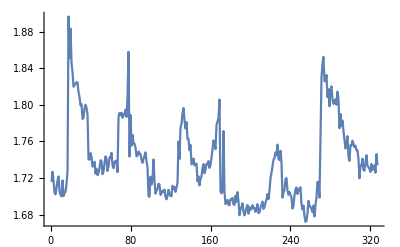

```mathematica
ListLinePlot[Norm/@First[Φ[{xs}]]]
```

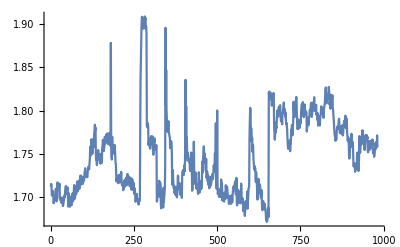

```mathematica
ListLinePlot[Norm/@(First@Φ[xs])]
```

```mathematica
exportFeatures[First@Φ[xs]]
```

/Users/TBM/Desktop/ProjetC/features.csv

```mathematica
Last@Φ[xs]
```

{0.30364,0.318253,0.320591,0.315376,0.313458,0.0261017,0.0401833,0.0453637,0.0411532,0.0457205,0.0474007,0.0480188,0.0421299,0.0460798,0.0475328,0.0480674,0.048264,0.0483364,0.0453049,0.0472478,0.0449044,0.0379261,0.0292428,0.0260483,0.0248732,0.0244408,0.0212237,0.0230983,0.0237879,0.0240416,0.0241349,0.0211112,0.0230569,0.0237727,0.024036,0.0241329,0.0241685,0.0241816,0.0241864,0.0241882,0.0211308,0.0230641,0.0237753,0.024037,0.0241332,0.0241686,0.0241817,0.0241865,0.0241882,0.0241889,0.0241891,0.0241892,0.0211311,0.0230642,0.0237754,0.024037,0.0210751,234.1,0.207221,0.212643,3.26901×10^7}

```mathematica
Last@xs
```

{0.0183156,1.,0.367879,0.135335,0.0497871,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,126.91,0.202359,0.208353,3.22744×10^7}

```mathematica
(Rest@Transpose@First[Φ[{xs}]])[[39]]
```

{-0.0647995,-0.0647993,-0.0647993,-0.0647993,-0.0647993,-0.0647993,-0.0647988,-0.0647988,-0.0647988,-0.0647988,-0.0647988,-0.0647973,-0.0647973,-0.0647973,-0.0647973,-0.0647935,-0.0647935,-0.0647935,-0.0647935,-0.0647935,-0.0647829,-0.0647829,-0.0647829,-0.0647829,-0.0647829,-0.0647542,-0.0647542,-0.0647542,-0.0647542,-0.0647542,-0.0646762,-0.0646762,-0.0646762,-0.0646762,-0.0644641,-0.0644641,-0.0644641,-0.0644641,-0.0644641,-0.0638877,-0.0638877,-0.0638877,-0.0638877,-0.0638877,-0.0623209,-0.0623209,-0.0623209,-0.0623209,-0.0623209,-0.0580617,-0.0580617,-0.0580617,-0.0580617,-0.0580617,-0.046484,-0.046484,-0.046484,-0.046484,-0.046484,-0.0150125,-0.0150125,-0.0150125,-0.0150125,0.0705357,0.0705357,0.0705357,0.0705357,0.0705357,0.30308,0.30308,0.30308,0.30308,0.30308,0.935201,0.935201}

```mathematica
MovingAverage
```

```mathematica
sample=Table[RandomInteger[{8,10}],{10}]
```

{8,8,8,9,10,10,8,10,9,9}

```mathematica
n=3;
(First@sample*ones[n-1])~Join~MovingAverage[sample,n]//N
Length[%]
```

{8.,8.,8.,8.33333,9.,9.66667,9.33333,9.33333,9.,9.33333}

10

```mathematica
MovingAverage[sample,n]//N
```

{8.,8.33333,9.,9.66667,9.33333,9.33333,9.,9.33333}

```mathematica
x[2015]["AAPL"]
```

Calling financial features feeds for AAPL

{{0.367879,0.135335,0.0497871,0.0183156,1.,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,108.9,0.242298,0.204525,8.,8.,8.,5.32046×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,105.832,0.243607,0.205911,8.,8.,8.,6.42855×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,105.842,0.261003,0.213181,8.,8.,8.,6.57971×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,107.326,0.251179,0.21304,8.,8.,8.,4.01059×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,111.45,0.249942,0.215241,8.,8.,8.,5.93645×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,111.57,0.28221,0.228814,8.,8.,8.,5.36995×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,108.821,0.282006,0.228571,8.,8.,8.,4.96508×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,109.787,0.290093,0.23584,8.,8.,8.,6.70919×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,109.368,0.286993,0.235715,8.,8.,8.,4.89566×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,106.4,0.28209,0.234148,8.,8.,8.,6.0014×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,105.573,0.286103,0.241885,8.,8.,8.,7.85133×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,108.293,0.261668,0.242404,8.,8.,8.,4.98999×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,109.119,0.280805,0.249331,8.,8.,8.,4.85759×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,111.958,0.279379,0.249849,8.,8.,8.,5.37964×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,112.536,0.2963,0.256445,8.,8.,8.,4.64648×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,112.655,0.296309,0.256104,8.,8.,8.,5.5615×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,108.711,0.289009,0.254215,8.,8.,8.,9.55687×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,114.857,0.316227,0.264905,8.,8.,8.,1.46477×10^8},{0.135335,0.0497871,0.0183156,1.,0.367879,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,118.433,0.375679,0.292242,8.,8.,8.,8.44364×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,116.699,0.381445,0.300242,8.,8.,8.,8.37455×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,118.164,0.384463,0.300966,110.585,8.,8.,6.27391×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,118.184,0.364871,0.301732,111.028,8.,8.,5.19157×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,119.09,0.364855,0.300108,111.659,8.,8.,7.01497×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,119.94,0.363613,0.30055,112.33,8.,8.,4.22462×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,118.93,0.342083,0.298115,112.883,8.,8.,4.3372×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,119.72,0.34492,0.298074,113.277,8.,8.,3.88898×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,122.02,0.327357,0.297249,113.774,8.,8.,6.20085×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,124.88,0.331101,0.300288,114.539,8.,8.,7.35618×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,126.46,0.334964,0.294248,115.333,8.,8.,7.44745×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,127.08,0.307888,0.294965,116.176,8.,8.,5.42722×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,127.83,0.301544,0.294275,117.197,8.,8.,6.31524×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,128.72,0.295666,0.2941,118.299,8.,8.,4.48917×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,128.45,0.295712,0.293915,119.259,8.,8.,3.73624×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,129.5,0.290633,0.288268,120.229,8.,8.,4.89484×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,133.,0.290537,0.28712,121.231,8.,8.,7.09741×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,132.17,0.297609,0.287628,122.166,8.,8.,6.92281×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,128.79,0.252015,0.288121,122.935,8.,8.,7.47117×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,130.42,0.221452,0.292104,123.968,8.,8.,9.12875×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,128.46,0.202253,0.290103,124.616,8.,8.,6.20148×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,129.09,0.202806,0.290558,125.124,8.,8.,4.80967×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,129.36,0.200795,0.286577,125.727,8.,8.,3.78163×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,128.54,0.200316,0.280326,126.221,118.403,8.,3.16663×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,126.41,0.203949,0.280066,126.612,118.82,8.,5.65171×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,126.6,0.216929,0.283014,126.97,119.314,8.,7.28421×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,127.14,0.212708,0.28269,127.313,119.822,8.,8.85285×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,124.51,0.212363,0.282222,127.579,120.231,8.,6.88566×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,122.24,0.220248,0.285041,127.699,120.488,8.,6.8939×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,124.45,0.213772,0.288686,127.814,120.794,8.,4.83627×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,123.59,0.219379,0.28923,127.753,121.146,8.,5.18273×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,124.95,0.219279,0.285796,127.681,121.507,8.,3.58743×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,127.04,0.222406,0.285078,127.679,121.928,8.,5.10231×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,128.47,0.229996,0.277268,127.71,122.453,8.,6.52709×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,127.5,0.233918,0.277647,127.651,122.975,8.,4.58095×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,125.9,0.233271,0.277875,127.53,123.394,8.,6.86951×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,127.21,0.211311,0.268655,127.421,123.825,8.,3.77097×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,126.69,0.216202,0.269222,127.12,124.176,8.,3.28423×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,123.38,0.196116,0.262045,126.702,124.434,8.,5.16552×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,124.24,0.209737,0.2701,126.485,124.71,8.,4.75729×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,123.25,0.207127,0.269906,126.144,125.056,8.,3.95462×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,126.37,0.206654,0.261986,126.044,125.33,8.,4.70997×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,124.43,0.229282,0.265423,125.822,125.473,8.,4.20906×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,124.25,0.234478,0.264022,125.579,125.653,8.,4.06214×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,125.32,0.227287,0.263961,125.426,125.823,120.744,3.22201×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,127.35,0.229783,0.258927,125.47,126.041,121.037,3.7194×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,126.01,0.23714,0.260736,125.442,126.206,121.357,3.50123×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,125.6,0.227115,0.262409,125.369,126.341,121.671,3.73292×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,126.56,0.215764,0.247701,125.467,126.523,121.976,3.2484×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,8.53305×10^-17,127.1,0.207858,0.216815,125.698,126.698,122.224,4.0188×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,126.85,0.205951,0.206502,125.812,126.813,122.467,3.63651×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,126.3,0.202986,0.203253,125.941,126.847,122.744,2.55246×10^7},{0.0497871,0.0183156,1.,0.367879,0.135335,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,126.78,0.194314,0.202151,126.029,126.855,123.014,2.88489×10^7},{0.135335,0.0497871,0.0183156,1.,0.367879,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,126.17,0.190003,0.202206,125.987,126.833,123.281,2.78953×10^7},{0.367879,0.135335,0.0497871,0.0183156,1.,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,2.31952×10^-16,124.75,0.188867,0.202173,125.81,126.76,123.572,5.13239×10^7},{1.,0.367879,0.135335,0.0497871,0.0183156,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,127.6,0.187752,0.203648,125.815,126.733,123.922,4.69344×10^7},{0.0183156,1.,0.367879,0.135335,0.0497871,2.31952×10^-16,8.53305×10^-17,3.13913×10^-17,1.15482×10^-17,4.24835×10^-18,1.56288×10^-18,5.74952×10^-19,2.11513×10^-19,7.78113×10^-20,2.86252×10^-20,1.05306×10^-20,3.874×10^-21,1.42516×10^-21,5.24289×10^-22,1.92875×10^-22,7.09547×10^-23,1.,0.367879,0.135335,0.0497871,0.0183156,0.00673795,0.00247875,0.000911882,0.000335463,0.00012341,0.0000453999,0.0000167017,6.14421×10^-6,2.26033×10^-6,8.31529×10^-7,3.05902×10^-7,1.12535×10^-7,4.13994×10^-8,1.523×10^-8,5.6028×10^-9,2.06115×10^-9,7.58256×10^-10,2.78947×10^-10,1.02619×10^-10,3.77513×10^-11,1.38879×10^-11,5.10909×10^-12,1.87953×10^-12,6.9144×10^-13,2.54367×10^-13,9.35762×10^-14,3.44248×10^-14,1.26642×10^-14,4.65889×10^-15,1.71391×10^-15,6.30512×10^-16,126.91,0.202359,0.208353,125.863,126.696,124.217,3.22744×10^7}}